```mathematica
g1=0.1;
g2=0.1 ;
gc=0.1 E^(I π/6);
m=({{0, g1, 0, 0}, {g1*, 0, gc, 0}, {0, gc*, 0, g2}, {0, 0, g2*, 0}});
eval=Eigensystem[m][[1]];
evec=Eigensystem[m][[2]];
n4=DiagonalMatrix[{1/evec[[1,4]],1/evec[[2,4]],1/evec[[3,4]],1/evec[[4,4]]}];
evec1=n4 . evec;
mm=Transpose[evec1];
ini={2,0,0,0};
dd=LinearSolve[mm,ini];
d[t_]:=Sum[dd[[i]]Exp[-I eval[[i]]t],{i,1,4}]
a[t_]:=Sum[mm[[1,i]]dd[[i]]Exp[-I eval[[i]]t],{i,1,4}]
b[t_]:=Sum[mm[[2,i]]dd[[i]]Exp[-I eval[[i]]t],{i,1,4}]
c[t_]:=Sum[mm[[3,i]]dd[[i]]Exp[-I eval[[i]]t],{i,1,4}]
```

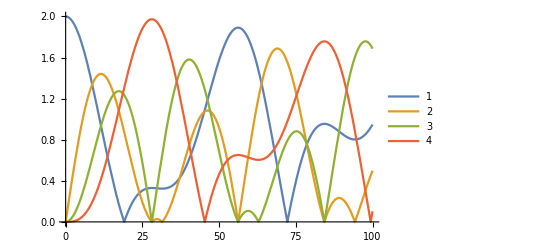

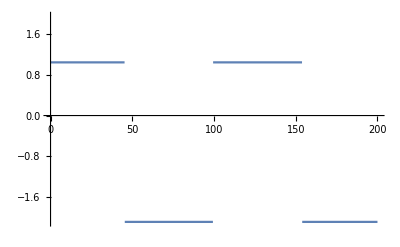

```mathematica
Plot[{Norm[a[t]],Norm[b[t]],Norm[c[t]],Norm[d[t]]},{t,0,100},PlotLegends->Automatic]
Plot[Arg[d[t]],{t,0,200},PlotLegends->Automatic]
```